# Числено решаване на обикновени диференциални уравнения

Дадени са следните задачи: (a и b са съответно предпоследната и последната цифра от факултетния номер)
a) y' = y - (2 + a)sinx, y(b) = a + b, x ∈ [b; b + 0.5]
б) y' = y - ln(x^2 + 1) + (2x)/(x^2 + 1) + b, y(a) = a + b, x ∈ [a; a + 1]
1. Да се намерят точните решения.
2. Да се решат по методите: Ойлер, модифициран Ойлер, Рунге-Кута (1, 1), Рунге-Кута (2/3, 2/3), Рунге-Кута с 4 междинни точки за а) при h = 0.1, 
за б) при n = 5. Да се направи сравнение между точното решение и численото приближение. Да се представи геометрична интерпретация на резултатите.
3. Колко би трябвало да са n и h за всеки един от посочените методи за всяка от задачите, за да се достигне точност за а) 10^-4, за б) 10^-7?

### 1. Да се намерят точните решения

Търсим общо решение:

```mathematica
Clear[x, y]
DSolve[y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 7, y[x], x]
```

{{y[x]→-7+ⅇ^x C[1]+Log[1+x^2]}}

Търсим частно решение:

```mathematica
Clear[x, y]
DSolve[{y'[x] ==y[x] - Log[x^2 + 1] + (2x)/(x^2 + 1) + 7, y[6] == 13}, y[x], x]
```

{{y[x]→(-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6}}

Визуализация на точното решение

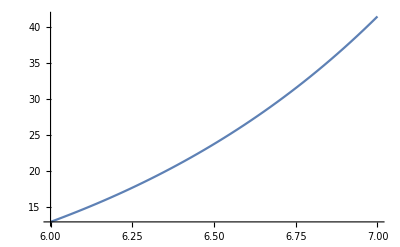

```mathematica
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
Plot[yt[x], {x,6,7}]
```

### 2. Да се реши по метода на Рунге-Кута с 4 междинни точки при h = 0.02:

#### 2.1. РК54 - Формула с четири междинни точки

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка  е 3.2×10^-9

Теоретичната глобална грешка е 1.6×10^-7

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 k_1 = 0.334268 k_2 = 0.337536 k_3 = 0.337568 k_4 = 0.34087 y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3376 f_i = 17.0435 k_1 = 0.340869 k_2 = 0.344203 k_3 = 0.344237 k_4 = 0.347605 y_точно = 13.3376 Истинска грешка = 4.36577×10^-10

i = 2 x_i = 6.04 y_i = 13.6818 f_i = 17.3802 k_1 = 0.347604 k_2 = 0.351006 k_3 = 0.35104 k_4 = 0.354476 y_точно = 13.6818 Истинска грешка = 8.90843×10^-10

i = 3 x_i = 6.06 y_i = 14.0328 f_i = 17.7238 k_1 = 0.354476 k_2 = 0.357947 k_3 = 0.357981 k_4 = 0.361488 y_точно = 14.0328 Истинска грешка = 1.36334×10^-9

i = 4 x_i = 6.08 y_i = 14.3908 f_i = 18.0744 k_1 = 0.361487 k_2 = 0.365028 k_3 = 0.365064 k_4 = 0.368641 y_точно = 14.3908 Истинска грешка = 1.85461×10^-9

i = 5 x_i = 6.1 y_i = 14.7558 f_i = 18.432 k_1 = 0.368641 k_2 = 0.372253 k_3 = 0.372289 k_4 = 0.375939 y_точно = 14.7558 Истинска грешка = 2.36522×10^-9

i = 6 x_i = 6.12 y_i = 15.1281 f_i = 18.7969 k_1 = 0.375939 k_2 = 0.379625 k_3 = 0.379662 k_4 = 0.383385 y_точно = 15.1281 Истинска грешка = 2.89576×10^-9

i = 7 x_i = 6.14 y_i = 15.5078 f_i = 19.1692 k_1 = 0.383385 k_2 = 0.387146 k_3 = 0.387183 k_4 = 0.390982 y_точно = 15.5078 Истинска грешка = 3.44682×10^-9

i = 8 x_i = 6.16 y_i = 15.8949 f_i = 19.5491 k_1 = 0.390982 k_2 = 0.394819 k_3 = 0.394857 k_4 = 0.398733 y_точно = 15.8949 Истинска грешка = 4.019×10^-9

i = 9 x_i = 6.18 y_i = 16.2898 f_i = 19.9367 k_1 = 0.398733 k_2 = 0.402648 k_3 = 0.402687 k_4 = 0.406642 y_точно = 16.2898 Истинска грешка = 4.61295×10^-9

i = 10 x_i = 6.2 y_i = 16.6925 f_i = 20.3321 k_1 = 0.406641 k_2 = 0.410635 k_3 = 0.410675 k_4 = 0.41471 y_точно = 16.6925 Истинска грешка = 5.2293×10^-9

i = 11 x_i = 6.22 y_i = 17.1031 f_i = 20.7355 k_1 = 0.41471 k_2 = 0.418785 k_3 = 0.418826 k_4 = 0.422942 y_точно = 17.1031 Истинска грешка = 5.86872×10^-9

i = 12 x_i = 6.24 y_i = 17.5219 f_i = 21.1471 k_1 = 0.422942 k_2 = 0.427099 k_3 = 0.427141 k_4 = 0.431341 y_точно = 17.5219 Истинска грешка = 6.53188×10^-9

i = 13 x_i = 6.26 y_i = 17.9491 f_i = 21.567 k_1 = 0.431341 k_2 = 0.435582 k_3 = 0.435625 k_4 = 0.43991 y_точно = 17.9491 Истинска грешка = 7.2195×10^-9

i = 14 x_i = 6.28 y_i = 18.3847 f_i = 21.9955 k_1 = 0.43991 k_2 = 0.444237 k_3 = 0.44428 k_4 = 0.448652 y_точно = 18.3847 Истинска грешка = 7.93228×10^-9

i = 15 x_i = 6.3 y_i = 18.8289 f_i = 22.4326 k_1 = 0.448652 k_2 = 0.453067 k_3 = 0.453112 k_4 = 0.457572 y_точно = 18.8289 Истинска грешка = 8.67095×10^-9

i = 16 x_i = 6.32 y_i = 19.282 f_i = 22.8786 k_1 = 0.457572 k_2 = 0.462076 k_3 = 0.462122 k_4 = 0.466672 y_точно = 19.282 Истинска грешка = 9.43627×10^-9

i = 17 x_i = 6.34 y_i = 19.7441 f_i = 23.3336 k_1 = 0.466672 k_2 = 0.471268 k_3 = 0.471314 k_4 = 0.475957 y_точно = 19.7441 Истинска грешка = 1.0229×10^-8

i = 18 x_i = 6.36 y_i = 20.2154 f_i = 23.7978 k_1 = 0.475957 k_2 = 0.480646 k_3 = 0.480693 k_4 = 0.48543 y_точно = 20.2154 Истинска грешка = 1.105×10^-8

i = 19 x_i = 6.38 y_i = 20.6961 f_i = 24.2715 k_1 = 0.485429 k_2 = 0.490213 k_3 = 0.490261 k_4 = 0.495094 y_точно = 20.6961 Истинска грешка = 1.19×10^-8

i = 20 x_i = 6.4 y_i = 21.1864 f_i = 24.7547 k_1 = 0.495094 k_2 = 0.499975 k_3 = 0.500024 k_4 = 0.504954 y_точно = 21.1864 Истинска грешка = 1.27799×10^-8

i = 21 x_i = 6.42 y_i = 21.6864 f_i = 25.2477 k_1 = 0.504954 k_2 = 0.509934 k_3 = 0.509984 k_4 = 0.515014 y_точно = 21.6864 Истинска грешка = 1.36906×10^-8

i = 22 x_i = 6.44 y_i = 22.1963 f_i = 25.7507 k_1 = 0.515014 k_2 = 0.520094 k_3 = 0.520145 k_4 = 0.525278 y_точно = 22.1963 Истинска грешка = 1.46328×10^-8

i = 23 x_i = 6.46 y_i = 22.7165 f_i = 26.2639 k_1 = 0.525277 k_2 = 0.530461 k_3 = 0.530513 k_4 = 0.535749 y_точно = 22.7165 Истинска грешка = 1.56076×10^-8

i = 24 x_i = 6.48 y_i = 23.247 f_i = 26.7874 k_1 = 0.535749 k_2 = 0.541037 k_3 = 0.54109 k_4 = 0.546432 y_точно = 23.247 Истинска грешка = 1.66159×10^-8

i = 25 x_i = 6.5 y_i = 23.788 f_i = 27.3216 k_1 = 0.546432 k_2 = 0.551828 k_3 = 0.551882 k_4 = 0.557332 y_точно = 23.788 Истинска грешка = 1.76585×10^-8

i = 26 x_i = 6.52 y_i = 24.3399 f_i = 27.8666 k_1 = 0.557332 k_2 = 0.562836 k_3 = 0.562891 k_4 = 0.568452 y_точно = 24.3399 Истинска грешка = 1.87366×10^-8

i = 27 x_i = 6.54 y_i = 24.9028 f_i = 28.4226 k_1 = 0.568452 k_2 = 0.574068 k_3 = 0.574124 k_4 = 0.579798 y_точно = 24.9028 Истинска грешка = 1.9851×10^-8

i = 28 x_i = 6.56 y_i = 25.4769 f_i = 28.9899 k_1 = 0.579797 k_2 = 0.585527 k_3 = 0.585584 k_4 = 0.591373 y_точно = 25.4769 Истинска грешка = 2.10029×10^-8

i = 29 x_i = 6.58 y_i = 26.0624 f_i = 29.5686 k_1 = 0.591372 k_2 = 0.597218 k_3 = 0.597277 k_4 = 0.603182 y_точно = 26.0624 Истинска грешка = 2.21932×10^-8

i = 30 x_i = 6.6 y_i = 26.6597 f_i = 30.1591 k_1 = 0.603182 k_2 = 0.609146 k_3 = 0.609205 k_4 = 0.61523 y_точно = 26.6597 Истинска грешка = 2.34231×10^-8

i = 31 x_i = 6.62 y_i = 27.2689 f_i = 30.7615 k_1 = 0.61523 k_2 = 0.621315 k_3 = 0.621376 k_4 = 0.627523 y_точно = 27.2689 Истинска грешка = 2.46937×10^-8

i = 32 x_i = 6.64 y_i = 27.8902 f_i = 31.3761 k_1 = 0.627522 k_2 = 0.63373 k_3 = 0.633792 k_4 = 0.640063 y_точно = 27.8902 Истинска грешка = 2.60061×10^-8

i = 33 x_i = 6.66 y_i = 28.524 f_i = 32.0031 k_1 = 0.640063 k_2 = 0.646397 k_3 = 0.64646 k_4 = 0.652858 y_точно = 28.524 Истинска грешка = 2.73615×10^-8

i = 34 x_i = 6.68 y_i = 29.1704 f_i = 32.6429 k_1 = 0.652858 k_2 = 0.659319 k_3 = 0.659384 k_4 = 0.665912 y_точно = 29.1704 Истинска грешка = 2.8761×10^-8

i = 35 x_i = 6.7 y_i = 29.8298 f_i = 33.2956 k_1 = 0.665911 k_2 = 0.672504 k_3 = 0.67257 k_4 = 0.679229 y_точно = 29.8298 Истинска грешка = 3.0206×10^-8

i = 36 x_i = 6.72 y_i = 30.5024 f_i = 33.9614 k_1 = 0.679229 k_2 = 0.685955 k_3 = 0.686022 k_4 = 0.692817 y_точно = 30.5024 Истинска грешка = 3.16977×10^-8

i = 37 x_i = 6.74 y_i = 31.1884 f_i = 34.6408 k_1 = 0.692816 k_2 = 0.699678 k_3 = 0.699747 k_4 = 0.706679 y_точно = 31.1884 Истинска грешка = 3.32374×10^-8

i = 38 x_i = 6.76 y_i = 31.8881 f_i = 35.3339 k_1 = 0.706678 k_2 = 0.713679 k_3 = 0.713749 k_4 = 0.720821 y_точно = 31.8881 Истинска грешка = 3.48263×10^-8

i = 39 x_i = 6.78 y_i = 32.6018 f_i = 36.041 k_1 = 0.720821 k_2 = 0.727963 k_3 = 0.728034 k_4 = 0.73525 y_точно = 32.6018 Истинска грешка = 3.6466×10^-8

i = 40 x_i = 6.8 y_i = 33.3298 f_i = 36.7625 k_1 = 0.735249 k_2 = 0.742536 k_3 = 0.742609 k_4 = 0.74997 y_точно = 33.3298 Истинска грешка = 3.81577×10^-8

i = 41 x_i = 6.82 y_i = 34.0724 f_i = 37.4985 k_1 = 0.74997 k_2 = 0.757404 k_3 = 0.757478 k_4 = 0.764989 y_точно = 34.0724 Истинска грешка = 3.99029×10^-8

i = 42 x_i = 6.84 y_i = 34.8299 f_i = 38.2494 k_1 = 0.764988 k_2 = 0.772573 k_3 = 0.772649 k_4 = 0.780311 y_точно = 34.8299 Истинска грешка = 4.17031×10^-8

i = 43 x_i = 6.86 y_i = 35.6025 f_i = 39.0155 k_1 = 0.78031 k_2 = 0.788048 k_3 = 0.788126 k_4 = 0.795943 y_точно = 35.6025 Истинска грешка = 4.35598×10^-8

i = 44 x_i = 6.88 y_i = 36.3906 f_i = 39.7971 k_1 = 0.795942 k_2 = 0.803837 k_3 = 0.803916 k_4 = 0.811891 y_точно = 36.3906 Истинска грешка = 4.54746×10^-8

i = 45 x_i = 6.9 y_i = 37.1945 f_i = 40.5945 k_1 = 0.811891 k_2 = 0.819945 k_3 = 0.820025 k_4 = 0.828162 y_точно = 37.1945 Истинска грешка = 4.74489×10^-8

i = 46 x_i = 6.92 y_i = 38.0145 f_i = 41.4081 k_1 = 0.828161 k_2 = 0.836379 k_3 = 0.836461 k_4 = 0.844762 y_точно = 38.0145 Истинска грешка = 4.94845×10^-8

i = 47 x_i = 6.94 y_i = 38.8509 f_i = 42.2381 k_1 = 0.844761 k_2 = 0.853145 k_3 = 0.853229 k_4 = 0.861698 y_точно = 38.8509 Истинска грешка = 5.1583×10^-8

i = 48 x_i = 6.96 y_i = 39.7041 f_i = 43.0849 k_1 = 0.861697 k_2 = 0.87025 k_3 = 0.870336 k_4 = 0.878976 y_точно = 39.7041 Истинска грешка = 5.37462×10^-8

i = 49 x_i = 6.98 y_i = 40.5744 f_i = 43.9488 k_1 = 0.878975 k_2 = 0.887701 k_3 = 0.887788 k_4 = 0.896603 y_точно = 40.5744 Истинска грешка = 5.59757×10^-8

i = 50 x_i = 7. y_i = 41.4622 f_i = 44.8301 k_1 = 0.896603 k_2 = 0.905505 k_3 = 0.905594 k_4 = 0.914588 y_точно = 41.4622 Истинска грешка = 5.82734×10^-8

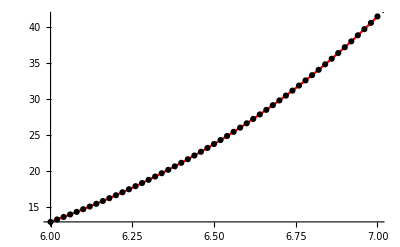

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=7;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
h = 0.02; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^5]
Print["Теоретичната глобална грешка е ", h^4]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
k1 = h *  f[x,y];
k2 = h *  f[x + h/2,y + k1/2];
k3 = h *  f[x + h/2,y + k2/2];
k4 = h *  f[x + h,y + k3];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " k_1 = ", k1, " k_2 = ", k2, " k_3 = ", k3, " k_4 = ", k4, " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y +1/6(k1 + 2k2 + 2k3 + k4);
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```

### 3. Колко би била точността при използване на модифицирания метод на Ойлер

#### 2.2. Модифициран метод на Ойлер

Мрежата е с n = 50. и стъпка h = 0.02

Теоретичната локална грешка  е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0 x_i = 6. y_i = 13. f_i = 16.7134 x_(i + 1/2) = 6.01 y_(i + 1/2) = 13.1671 f_(i + 1/2) = 16.8768  y_точно = 13. Истинска грешка = 0.

i = 1 x_i = 6.02 y_i = 13.3375 f_i = 17.0434 x_(i + 1/2) = 6.03 y_(i + 1/2) = 13.508 f_(i + 1/2) = 17.2101  y_точно = 13.3376 Истинска грешка = 0.0000219159

i = 2 x_i = 6.04 y_i = 13.6817 f_i = 17.3802 x_(i + 1/2) = 6.05 y_(i + 1/2) = 13.8555 f_(i + 1/2) = 17.5503  y_точно = 13.6818 Истинска грешка = 0.0000447185

i = 3 x_i = 6.06 y_i = 14.0327 f_i = 17.7237 x_(i + 1/2) = 6.07 y_(i + 1/2) = 14.21 f_(i + 1/2) = 17.8973  y_точно = 14.0328 Истинска грешка = 0.0000684345

i = 4 x_i = 6.08 y_i = 14.3907 f_i = 18.0743 x_(i + 1/2) = 6.09 y_(i + 1/2) = 14.5714 f_(i + 1/2) = 18.2513  y_точно = 14.3908 Истинска грешка = 0.0000930916

i = 5 x_i = 6.1 y_i = 14.7557 f_i = 18.4319 x_(i + 1/2) = 6.11 y_(i + 1/2) = 14.94 f_(i + 1/2) = 18.6125  y_точно = 14.7558 Истинска грешка = 0.000118718

i = 6 x_i = 6.12 y_i = 15.128 f_i = 18.7968 x_(i + 1/2) = 6.13 y_(i + 1/2) = 15.3159 f_(i + 1/2) = 18.9811  y_точно = 15.1281 Истинска грешка = 0.000145343

i = 7 x_i = 6.14 y_i = 15.5076 f_i = 19.1691 x_(i + 1/2) = 6.15 y_(i + 1/2) = 15.6993 f_(i + 1/2) = 19.3571  y_точно = 15.5078 Истинска грешка = 0.000172997

i = 8 x_i = 6.16 y_i = 15.8947 f_i = 19.5489 x_(i + 1/2) = 6.17 y_(i + 1/2) = 16.0902 f_(i + 1/2) = 19.7407  y_точно = 15.8949 Истинска грешка = 0.000201709

i = 9 x_i = 6.18 y_i = 16.2895 f_i = 19.9364 x_(i + 1/2) = 6.19 y_(i + 1/2) = 16.4889 f_(i + 1/2) = 20.1322  y_точно = 16.2898 Истинска грешка = 0.000231512

i = 10 x_i = 6.2 y_i = 16.6922 f_i = 20.3318 x_(i + 1/2) = 6.21 y_(i + 1/2) = 16.8955 f_(i + 1/2) = 20.5315  y_точно = 16.6925 Истинска грешка = 0.000262438

i = 11 x_i = 6.22 y_i = 17.1028 f_i = 20.7352 x_(i + 1/2) = 6.23 y_(i + 1/2) = 17.3102 f_(i + 1/2) = 20.9389  y_точно = 17.1031 Истинска грешка = 0.000294521

i = 12 x_i = 6.24 y_i = 17.5216 f_i = 21.1468 x_(i + 1/2) = 6.25 y_(i + 1/2) = 17.7331 f_(i + 1/2) = 21.3546  y_точно = 17.5219 Истинска грешка = 0.000327793

i = 13 x_i = 6.26 y_i = 17.9487 f_i = 21.5667 x_(i + 1/2) = 6.27 y_(i + 1/2) = 18.1644 f_(i + 1/2) = 21.7788  y_точно = 17.9491 Истинска грешка = 0.00036229

i = 14 x_i = 6.28 y_i = 18.3843 f_i = 21.9951 x_(i + 1/2) = 6.29 y_(i + 1/2) = 18.6042 f_(i + 1/2) = 22.2115  y_точно = 18.3847 Истинска грешка = 0.000398049

i = 15 x_i = 6.3 y_i = 18.8285 f_i = 22.4322 x_(i + 1/2) = 6.31 y_(i + 1/2) = 19.0528 f_(i + 1/2) = 22.6529  y_точно = 18.8289 Истинска грешка = 0.000435105

i = 16 x_i = 6.32 y_i = 19.2816 f_i = 22.8781 x_(i + 1/2) = 6.33 y_(i + 1/2) = 19.5103 f_(i + 1/2) = 23.1033  y_точно = 19.282 Истинска грешка = 0.000473498

i = 17 x_i = 6.34 y_i = 19.7436 f_i = 23.3331 x_(i + 1/2) = 6.35 y_(i + 1/2) = 19.977 f_(i + 1/2) = 23.5629  y_точно = 19.7441 Истинска грешка = 0.000513265

i = 18 x_i = 6.36 y_i = 20.2149 f_i = 23.7973 x_(i + 1/2) = 6.37 y_(i + 1/2) = 20.4528 f_(i + 1/2) = 24.0317  y_точно = 20.2154 Истинска грешка = 0.000554446

i = 19 x_i = 6.38 y_i = 20.6955 f_i = 24.2709 x_(i + 1/2) = 6.39 y_(i + 1/2) = 20.9382 f_(i + 1/2) = 24.5101  y_точно = 20.6961 Истинска грешка = 0.000597083

i = 20 x_i = 6.4 y_i = 21.1857 f_i = 24.754 x_(i + 1/2) = 6.41 y_(i + 1/2) = 21.4333 f_(i + 1/2) = 24.9981  y_точно = 21.1864 Истинска грешка = 0.000641217

i = 21 x_i = 6.42 y_i = 21.6857 f_i = 25.247 x_(i + 1/2) = 6.43 y_(i + 1/2) = 21.9381 f_(i + 1/2) = 25.496  y_точно = 21.6864 Истинска грешка = 0.000686892

i = 22 x_i = 6.44 y_i = 22.1956 f_i = 25.75 x_(i + 1/2) = 6.45 y_(i + 1/2) = 22.4531 f_(i + 1/2) = 26.004  y_точно = 22.1963 Истинска грешка = 0.000734152

i = 23 x_i = 6.46 y_i = 22.7157 f_i = 26.2631 x_(i + 1/2) = 6.47 y_(i + 1/2) = 22.9783 f_(i + 1/2) = 26.5223  y_точно = 22.7165 Истинска грешка = 0.000783041

i = 24 x_i = 6.48 y_i = 23.2461 f_i = 26.7866 x_(i + 1/2) = 6.49 y_(i + 1/2) = 23.514 f_(i + 1/2) = 27.051  y_точно = 23.247 Истинска грешка = 0.000833608

i = 25 x_i = 6.5 y_i = 23.7871 f_i = 27.3207 x_(i + 1/2) = 6.51 y_(i + 1/2) = 24.0603 f_(i + 1/2) = 27.5905  y_точно = 23.788 Истинска грешка = 0.000885898

i = 26 x_i = 6.52 y_i = 24.3389 f_i = 27.8656 x_(i + 1/2) = 6.53 y_(i + 1/2) = 24.6176 f_(i + 1/2) = 28.1409  y_точно = 24.3399 Истинска грешка = 0.000939962

i = 27 x_i = 6.54 y_i = 24.9018 f_i = 28.4216 x_(i + 1/2) = 6.55 y_(i + 1/2) = 25.186 f_(i + 1/2) = 28.7024  y_точно = 24.9028 Истинска грешка = 0.00099585

i = 28 x_i = 6.56 y_i = 25.4758 f_i = 28.9888 x_(i + 1/2) = 6.57 y_(i + 1/2) = 25.7657 f_(i + 1/2) = 29.2753  y_точно = 25.4769 Истинска грешка = 0.00105361

i = 29 x_i = 6.58 y_i = 26.0613 f_i = 29.5675 x_(i + 1/2) = 6.59 y_(i + 1/2) = 26.357 f_(i + 1/2) = 29.8598  y_точно = 26.0624 Истинска грешка = 0.00111331

i = 30 x_i = 6.6 y_i = 26.6585 f_i = 30.1579 x_(i + 1/2) = 6.61 y_(i + 1/2) = 26.9601 f_(i + 1/2) = 30.4561  y_точно = 26.6597 Истинска грешка = 0.00117498

i = 31 x_i = 6.62 y_i = 27.2676 f_i = 30.7603 x_(i + 1/2) = 6.63 y_(i + 1/2) = 27.5752 f_(i + 1/2) = 31.0645  y_точно = 27.2689 Истинска грешка = 0.00123869

i = 32 x_i = 6.64 y_i = 27.8889 f_i = 31.3748 x_(i + 1/2) = 6.65 y_(i + 1/2) = 28.2027 f_(i + 1/2) = 31.6852  y_точно = 27.8902 Истинска грешка = 0.0013045

i = 33 x_i = 6.66 y_i = 28.5226 f_i = 32.0018 x_(i + 1/2) = 6.67 y_(i + 1/2) = 28.8426 f_(i + 1/2) = 32.3184  y_точно = 28.524 Истинска грешка = 0.00137246

i = 34 x_i = 6.68 y_i = 29.169 f_i = 32.6414 x_(i + 1/2) = 6.69 y_(i + 1/2) = 29.4954 f_(i + 1/2) = 32.9645  y_точно = 29.1704 Истинска грешка = 0.00144264

i = 35 x_i = 6.7 y_i = 29.8283 f_i = 33.294 x_(i + 1/2) = 6.71 y_(i + 1/2) = 30.1612 f_(i + 1/2) = 33.6237  y_точно = 29.8298 Истинска грешка = 0.00151509

i = 36 x_i = 6.72 y_i = 30.5008 f_i = 33.9599 x_(i + 1/2) = 6.73 y_(i + 1/2) = 30.8404 f_(i + 1/2) = 34.2961  y_точно = 30.5024 Истинска грешка = 0.00158989

i = 37 x_i = 6.74 y_i = 31.1867 f_i = 34.6391 x_(i + 1/2) = 6.75 y_(i + 1/2) = 31.5331 f_(i + 1/2) = 34.9822  y_точно = 31.1884 Истинска грешка = 0.00166708

i = 38 x_i = 6.76 y_i = 31.8863 f_i = 35.3322 x_(i + 1/2) = 6.77 y_(i + 1/2) = 32.2397 f_(i + 1/2) = 35.6822  y_точно = 31.8881 Истинска грешка = 0.00174675

i = 39 x_i = 6.78 y_i = 32.6 f_i = 36.0392 x_(i + 1/2) = 6.79 y_(i + 1/2) = 32.9604 f_(i + 1/2) = 36.3963  y_точно = 32.6018 Истинска грешка = 0.00182896

i = 40 x_i = 6.8 y_i = 33.3279 f_i = 36.7606 x_(i + 1/2) = 6.81 y_(i + 1/2) = 33.6955 f_(i + 1/2) = 37.1249  y_точно = 33.3298 Истинска грешка = 0.00191378

i = 41 x_i = 6.82 y_i = 34.0704 f_i = 37.4965 x_(i + 1/2) = 6.83 y_(i + 1/2) = 34.4454 f_(i + 1/2) = 37.8682  y_точно = 34.0724 Истинска грешка = 0.00200128

i = 42 x_i = 6.84 y_i = 34.8278 f_i = 38.2473 x_(i + 1/2) = 6.85 y_(i + 1/2) = 35.2102 f_(i + 1/2) = 38.6265  y_точно = 34.8299 Истинска грешка = 0.00209153

i = 43 x_i = 6.86 y_i = 35.6003 f_i = 39.0133 x_(i + 1/2) = 6.87 y_(i + 1/2) = 35.9904 f_(i + 1/2) = 39.4002  y_точно = 35.6025 Истинска грешка = 0.00218461

i = 44 x_i = 6.88 y_i = 36.3883 f_i = 39.7948 x_(i + 1/2) = 6.89 y_(i + 1/2) = 36.7862 f_(i + 1/2) = 40.1895  y_точно = 36.3906 Истинска грешка = 0.00228061

i = 45 x_i = 6.9 y_i = 37.1921 f_i = 40.5921 x_(i + 1/2) = 6.91 y_(i + 1/2) = 37.598 f_(i + 1/2) = 40.9948  y_точно = 37.1945 Истинска грешка = 0.00237958

i = 46 x_i = 6.92 y_i = 38.012 f_i = 41.4056 x_(i + 1/2) = 6.93 y_(i + 1/2) = 38.426 f_(i + 1/2) = 41.8164  y_точно = 38.0145 Истинска грешка = 0.00248163

i = 47 x_i = 6.94 y_i = 38.8483 f_i = 42.2355 x_(i + 1/2) = 6.95 y_(i + 1/2) = 39.2707 f_(i + 1/2) = 42.6546  y_точно = 38.8509 Истинска грешка = 0.00258684

i = 48 x_i = 6.96 y_i = 39.7014 f_i = 43.0822 x_(i + 1/2) = 6.97 y_(i + 1/2) = 40.1322 f_(i + 1/2) = 43.5098  y_точно = 39.7041 Истинска грешка = 0.00269528

i = 49 x_i = 6.98 y_i = 40.5716 f_i = 43.946 x_(i + 1/2) = 6.99 y_(i + 1/2) = 41.0111 f_(i + 1/2) = 44.3822  y_точно = 40.5744 Истинска грешка = 0.00280704

i = 50 x_i = 7. y_i = 41.4592 f_i = 44.8272 x_(i + 1/2) = 7.01 y_(i + 1/2) = 41.9075 f_(i + 1/2) = 45.2723  y_точно = 41.4622 Истинска грешка = 0.00292223

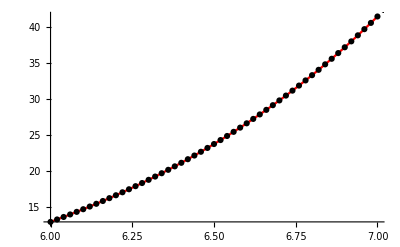

```mathematica
(*Въвеждаме услонието на задачата*)
a = 6.;b=7;
x = a;
y =13.;
points = {{x,y}};
f[x_,y_] := y- Log[x^2 + 1] + (2x)/(x^2 + 1) + 7
(*Точно решение*)
yt[x_] := (-7 ⅇ^6+20 ⅇ^x-ⅇ^x Log[37]+ⅇ^6 Log[1+x^2])/ⅇ^6
(*Съставяме мрежата*)
h = 0.02; n = (b - a)/h;
Print["Мрежата е с n = ", n , " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
x12 = x + h/2;
y12 = y + h/2 f[x,y];
Print["i = ", i, " x_i = ", x, " y_i = ", y, " f_i = ", f[x,y]  , " x_(i + 1/2) = ", x12, " y_(i + 1/2) = ", y12, " f_(i + 1/2) = ", f[x12,y12]  " y_(:0442:043e:0447:043d:043e) = ", yt[x], " Истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x12,y12];
x = x + h;
AppendTo[points, {x,y}]
]
(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle-> Black];
Show[gryt, grp]
```